```mathematica
ClearAll["Global`*"]
```

# Constants

```mathematica
e = 1.60217657 10^-19;
ϵ0 = 8.85418782 10^-12;
μB = 9.27400968 10^-24;
ℏ = 1.054571726 10^-34;
kB = 1.380648 10^-23;
m = 2.838464 10^-25;
```

```mathematica
7^2 0.62
```

30.38

```mathematica
7 6.20
```

43.4

# Find Parameters

```mathematica
Clear[η]
```

```mathematica
η[23.6, 2 π 267.75 10^3]
```

0.00916655

### Input

```mathematica
dzB = 23.6;
ν = 2 π 221.02 10^3;
ωp1 = 2 π 109624.791 10^3;
ωp2 = 2 π 112851.355 10^3 ;
```

### Spatial Extent

```mathematica
Δz[ν_] :=  2* 1/2^(2/3)(e^2/(4 π ϵ0 m ν^2))^(1/3);
```

### Lamb - Dicke Parameter

```mathematica
η[dzB_, ν_]:=1/(√2)(μB dzB)/(ℏ ν)  √(ℏ/(2 m ν)); (* Page 91 of Joe's Thesis *)
```

### Gradient

```mathematica
δzB[Δz_, Δω_] := (ℏ Δω)/(μB Δz);
```

### Output

```mathematica
Dataset[{{"Secular Frequency", "ν", ν/(2 π 10^3), "KHz"}, {"Frequency difference", "Δω", (ωp2-ωp1)/(2 π 10^3), "KHz"}, {"Spatial extent", "Δz", Δz[ν] 10^6, "μm"},
{"Gradient", "δzB", δzB[Δz[ν], ωp2 - ωp1], "μm"},{"Lamb-Dicke Parameter (COM)", "η", η[dzB, ν], ""}, {"Lamb-Dicke Parameter (STR)", "η", η[dzB, ν*√3], ""}}]
```

# Find frequencies:

### Input

```mathematica
VSGfreq = 12.542812118500 10^9;
ω0 =  100015.358 10^3 + VSGfreq;
```

### Output

```mathematica
ωhf = VSGfreq + 10^8;

χ =√((ω0/ωhf)^2 - 1);
 ωp = ωhf/2(1 + χ - √(1 + χ^2)) ;
ωm = -ωhf/2(1 - χ - √(1 + χ^2));
ωplus  = (ω0 - VSGfreq + ωp )/ 10^3 + 50;
ωminus = (ω0 - VSGfreq - ωm )/ 10^3 - 50;

Dataset[{{"Clock Frequency", "ω_0", (ω0 - VSGfreq)/10^3, "KHz"}, {"Plus Frequency", "ω_+", ωplus, "KHz"}, {"Minus Frequency", "ω_-", ωminus, "KHz"}}]
```

```mathematica
109057.791 10^3-465.690 10^3
```

1.08592×10^8

```mathematica
Evaluate[109057791+465690]
```

109523481

```mathematica
((ℏ ωhf)/μB √((ω0/ωhf)^2 - 1)) 10^4
(ω0/ωhf)^2 - 1
(ℏ ωhf)/μB
```

2.36736

2.71158×10^-6

0.143765

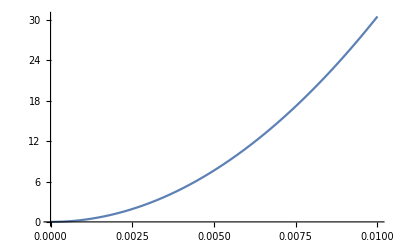

```mathematica
Plot[(ωhf √(1 +((μB B)/(ℏ ωhf))^2) - ωhf)/10^6, {B, 0, 100 10^-4}]
```